```mathematica
RowDelete[x_,entries_]:=Module[{list,i},
list=Table[{entries[[i]]},{i,1,Length[entries]}];
Delete[x,list]
]
(*ColumnDelete takes a matrix and delete the specified columns*)
ColumnDelete[x_,entries_]:=Module[{},
Transpose[RowDelete[Transpose[x],entries]]
]
(*AddZeroToRow adds a zero to a row vector*)
AddZeroToRow[x_,j_]:=Module[{l},
l=Length[x];
Join[Take[x,j-1],{0},Take[x,-(l-j+1)]]
]
(*AddZerosToRow will add any number of zeros to a row vector*)
AddZerosToRow[x_,entries_]:=Module[{y,list,i},
y=x;
list=Sort[entries];
For[i=1,i≤Length[list],i++,
y=AddZeroToRow[y,list[[i]]]
];
y
]


MAR[datasets_, cov_, constraints_]:=Module[{X,U,Y,Z,D,d0,p,x0,u0,y0,one,popdata,covdata,tanks,tankrow,index,tempdata,c,j,k},
p=Length[datasets[[1,1]]]-cov;

If[cov==0,
X={};Y={};
For[j=1,j≤Length[datasets],j++,
x0=Delete[datasets[[j]],Length[datasets[[j]]]];
y0=Delete[datasets[[j]],1];
X=Join[X,x0];
Y=Join[Y,y0]
];
one={Table[1,{i,1,Length[X]}]};
Z=Transpose[Join[one,Transpose[X]]];
D={};
For[k=1,k≤p,k++,
c={};
For[j=1,j≤p,j++,
c=Join[c,If[MemberQ[constraints,{k,j}],{j},{}]]
];
d0={AddZerosToRow[Flatten[{Y[[All,k]]}.ColumnDelete[Z,c+1].Inverse[Transpose[ColumnDelete[Z,c+1]].ColumnDelete[Z,c+1]]],c+1]};
D=Join[D,d0]
];
D,

X={};Y={};U={};
For[j=1,j≤Length[datasets],j++,
tempdata=datasets[[j]];
x0=tempdata[[All,cov+1;;cov+p]];
x0=Delete[x0,Length[x0]];
u0=tempdata[[All,1;;cov]];
u0=Delete[u0,Length[u0]];
y0=tempdata[[All,cov+1;;cov+p]];
y0=Delete[y0,1];

X=Join[X,x0];
U=Join[U,u0];
Y=Join[Y,y0];
];
one={Table[1,{i,1,Length[X]}]};
Z=Transpose[Join[one,Transpose[U],Transpose[X]]];
D={};
For[k=1,k≤p,k++,
c={};
For[j=1,j≤p,j++,
c=Join[c,If[MemberQ[constraints,{k,j}],{j},{}]]
];
d0={AddZerosToRow[Flatten[{Y[[All,k]]}.ColumnDelete[Z,c+1+cov].Inverse[Transpose[ColumnDelete[Z,c+1+cov]].ColumnDelete[Z,c+1+cov]]],c+1+cov]};
D=Join[D,d0]
];
D
]
]


ProcessData[raw_,cov_]:=Module[{rawdata,p,tankrow,tanks,purepopdata,logpopdata,covdata,processeddata,index,compdataset,i,i0,j,data},
rawdata=Delete[raw,1];
p=Length[rawdata[[1]]]-cov-1;

tankrow=Delete[raw[[All,1]],1];(*extracts the column of tank labels as a row vector.*)
tanks=DeleteDuplicates[tankrow];(*Just getting a list of tank labels*)

purepopdata=ColumnDelete[rawdata,{1}];
For[i=1,i≤cov,i++,
purepopdata=ColumnDelete[purepopdata,{1}]
];
logpopdata=Log[purepopdata];

If[cov==0,covdata={},
covdata=ColumnDelete[rawdata,{1}];
For[i=1,i≤p,i++,
covdata=ColumnDelete[covdata,{Length[covdata[[1]]]}]
]
];

processeddata=If[cov==0,Transpose[Join[{tankrow},Transpose[logpopdata]]],Transpose[Join[{tankrow},Transpose[covdata],Transpose[logpopdata]]]];(*Join log transformed values back up with tank labels*)

(*Below we extract tank specific processed data and label it by the tank label.*)
For[j=1,j≤Length[tanks],j++,
index=tanks[[j]];
data[index]={};
For[i=1,i≤Length[processeddata],i++,
i0=If[processeddata[[i,1]]==index,{processeddata[[i]]},{}];
data[index]=Join[data[index],i0]
];
data[index]=ColumnDelete[data[index],{1}]
];

compdataset={};
For[j=1,j≤Length[tanks],j++,
index=tanks[[j]];
compdataset=Join[compdataset,{data[index]}]
];
compdataset
]
```

```mathematica
SetDirectory["/Users/4/Documents/Weak interactions/tank data"];
rawdata[1]=Import["CER0.csv"];
rawdata[2]=Import["CER_DAP0.csv"];
rawdata[3]=Import["CER_SCA0.csv"];
rawdata[4]=Import["DAP0.csv"];
rawdata[5]=Import["DAPSCA0.csv"];
rawdata[6]=Import["SCA0.csv"];
rawdata[7]=Import["N0.csv"];
rawdata[8]=Import["N_CER0.csv"];
rawdata[9]=Import["N_CER_DAP0.csv"];
rawdata[10]=Import["N_CER_SCA0.csv"];
rawdata[11]=Import["N_DAP0.csv"];
rawdata[12]=Import["N_SCA0.csv"];
rawdata[13]=Import["N_SCA_DAP0.csv"];
rawdata[14]=Import["N_I_DAP0.csv"];
rawdata[15]=Import["N_I0.csv"];
rawdata[16]=Import["N_I_COP0.csv"];
rawdata[17]=Import["CER_SCA_DAP0.csv"];

(*1 covariate*)
rawdata[18]=Import["CER.csv"];
rawdata[19]=Import["CER_DAP.csv"];
rawdata[20]=Import["CER_SCA.csv"];
rawdata[21]=Import["DAP.csv"];
rawdata[22]=Import["DAPSCA.csv"];
rawdata[23]=Import["SCA.csv"];
rawdata[24]=Import["N.csv"];
rawdata[25]=Import["N_CER.csv"];
rawdata[26]=Import["N_CER_DAP.csv"];
rawdata[27]=Import["N_CER_SCA.csv"];
rawdata[28]=Import["N_Dap.csv"];
rawdata[29]=Import["N_Sca.csv"];
rawdata[30]=Import["N_SCA_DAP.csv"];
rawdata[31]=Import["N_I_DAP.csv"];

(*2 covariates*)
rawdata[32]=Import["N_I.csv"];
rawdata[33]=Import["N_I_cop.csv"];

For[i=1,i≤17,i++,
prodata[i]=ProcessData[rawdata[i],0];
m[i]=MAR[prodata[i],0,{}]
]
For[i=18,i≤33,i++,
prodata[i] = ProcessData[rawdata[i],1];
m[i]=MAR[prodata[i],1,{}]
]
```

```mathematica
(*Find distribution of B matrices (for off-diagonal and on-diagonal) and produce some new B matrices to use as "known" B matrices*)
(*Find covariance matrix of Sigma for the data and use that to produce noise*)
(*Refer to picture on your phone*)
(*Actual data took 26 samples from 6 tanks*)
(*Standard deviation for estimated B matrix should be smaller than known B matrix and tests for stability should be the similar if good estimate*)
```

```mathematica
B[D_]:=Module[{p,cov,B},(*extract B matrix*)
p=Length[D];
cov=Length[D[[1]]]-p-1;
B=D[[All,2+cov;;1+cov+p]]
]
```

```mathematica
For[i=1,i≤17,i++,
p=Length[m[i]];
cov=Length[m[i][[1]]]-p-1;
Amatrix[i] = m[i][[All,1;;1]];
Bmatrix[i] = B[m[i]];
If[cov == 0,
Cmatrix[i] = 0,
Cmatrix[i] = m[i][[All,2;;2+cov-1]]]
]
prodata[1][[1]]
```

{{-3.7966,4.2223,2.33311},{-3.7966,4.67227,-5.29832},{-3.7966,5.59827,3.31273},{-3.7966,4.61542,1.14422},{-0.890054,4.5743,2.7447},{-0.786299,4.65053,1.43031},{-3.7966,4.4666,2.14593},{-0.786299,4.4666,2.14593},{-3.7966,3.00618,0.524729},{-3.7966,3.26995,1.10856},{-3.7966,3.11928,2.1883},{0.523206,3.35446,1.19089},{1.08662,2.99423,2.42392},{1.29314,3.00964,0.722706},{1.40771,3.4128,-5.29832},{2.14771,3.59759,0.392042},{1.64808,4.0189,1.71019},{2.8311,3.95623,2.26696},{0.716171,3.99434,1.81156},{-3.7966,3.91681,1.51513},{-3.7966,3.77826,0.139762},{-0.196907,3.89304,3.13157},{-1.71716,3.55506,0.8671},{-3.10345,3.23514,0.0953102},{-3.7966,5.28973,3.8582},{-2.00484,3.25771,-1.89712}}

```mathematica
For[i=1,i≤17,i++,
noise[i] = {};
For[j=1,j≤Length[prodata[i]],j++,
noiseprep1[j]={};
noiseprep2[j]={};
For[k=1,k≤Length[prodata[i][[j]]]-1,k++,
noiseprep1[j] = Join[noiseprep1[j],{prodata[i][[j,k+1]]-Amatrix[i]-Bmatrix[i].prodata[i][[j,k]]}];
noiseprep2[j] = Join[noiseprep2[j],Transpose[noiseprep1[j][[k]]]]
];
noise[i] =Join[noise[i],{noiseprep2[j]}]
];
covar[i]={};
For[j=1,j≤Length[noise[i]],j++,
covar[i]=Join[covar[i],{Covariance[noise[i][[j]]]}]
]
]
covar[1]
```

{{{3.41615,-0.00477982,0.290084},{-0.00477982,0.401376,0.421965},{0.290084,0.421965,5.28084}},{{3.76481,-0.194817,-0.0538784},{-0.194817,1.35703,1.01786},{-0.0538784,1.01786,1.72787}},{{8.35667,0.101928,-0.260362},{0.101928,0.807912,0.54894},{-0.260362,0.54894,0.91344}},{{4.46718,-0.593411,-0.824836},{-0.593411,1.15659,-0.0730475},{-0.824836,-0.0730475,5.43734}},{{7.14908,0.518367,3.35394},{0.518367,1.37325,1.70133},{3.35394,1.70133,6.34407}},{{6.99683,0.564151,0.486896},{0.564151,0.659561,0.521248},{0.486896,0.521248,1.25276}}}

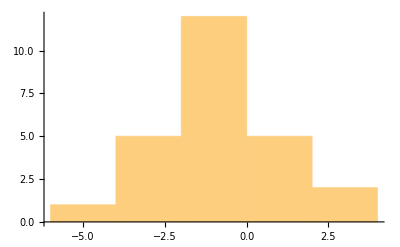

1.84828

```mathematica
Histogram[noise[1][[1,All,1]]]
StandardDeviation[noise[1][[1,All,1]]]
```

```mathematica
(*Using all B matrices*)
odlist = {};
dlist={};
For[i=1,i≤17,i++,
For[j=1,j≤Length[Bmatrix[i]],j++,
For[k=1,k≤Length[Bmatrix[i][[j]]],k++,
If[j≠k,
odlist = Join[odlist,{Bmatrix[i][[j,k]]}],
dlist = Join[dlist,{Bmatrix[i][[j,k]]}]
]
]
]
]
```

```mathematica
(*Using one Bmatrix*)
odlist={};
dlist={};
For[i=1,i≤Length[Bmatrix[1]],i++,
For[j=1,j≤Length[Bmatrix[1][[i]]],j++,
If[i==j,
dlist = Join[dlist,{Bmatrix[1][[i,j]]}],
odlist = Join[odlist,{Bmatrix[1][[i,j]]}]
]
]
]
```

```mathematica
numB = 100;
For[i=1,i≤numB,i++,
For[j=1,j≤3,j++,
For[k=1,k≤3,k++,
If[j≠k,
Bmat[j,k]=RandomVariate[NormalDistribution[Bmatrix[1][[j,k]],StandardDeviation[odlist]]],
Bmat[j,k]=RandomVariate[NormalDistribution[Bmatrix[1][[j,k]],StandardDeviation[dlist]]]
]
]
];
TestB[i] = Array[Bmat,{3,3}]
]
(*For[i=1,i≤117,i++,
If[i≤17,
allB[i] = Bmatrix[i],
allB[i] = TestB[i-17]
]
]*)
```

```mathematica
(* Takes hours to run before computer runs out of memory and wipes out data
For[i=1,i≤117,i++,
Sigma[1] = Array[elem,{Length[allB[1][[1]]],Length[allB[1][[1]]]}];
For[j=1,j≤3,j++,
For[k=1,k≤3,k++,
elem[j,k]=RandomReal[{-1,1}];
elem[k,j]=elem[j,k];
]
];
Sigma[1] = Sigma[1].Transpose[Sigma[1]];
Et[i] = RandomReal[{-1,1},{maxt,Length[allB[i][[1]]]}].CholeskyDecomposition[Sigma[i]];
Xlist[i] = {};
For[l=1,l≤ Length[prodata[i]],l++,
prep2 = {};
X[0] = prodata[i][[l,1]];
maxt = 1000;
For[m=1,m≤maxt,m++,
X[m] = allB[i].X[m-1]+Transpose[{Et[i][[m]]}];
prep1 = {};
For[n=1,n≤Length[X[m]],n++,
prep1 = Join[prep1,X[m][[n]]];
];
prep2 = Join[prep2,{prep1}];
];
Xlist[i] = Join[Xlist[i],{prep2}];
];
Bmatrix2[i]=B[MAR[Xlist[i],0,{}]]
]*)
```

```mathematica
(*Only uses B matrices that were produced from the statistical properties of the B matrices from the data*)
maxt = 50;
iter = 50;
For[i=1,i≤numB,i++,
Sigma[i] = Array[elem,{Length[TestB[i][[1]]],Length[TestB[i][[1]]]}];
For[j=1,j≤3,j++,
For[k=1,k≤3,k++,
elem[j,k]=RandomReal[{-1,1}];
elem[k,j]=elem[j,k];
]
];
Sigma[i] = Sigma[i].Transpose[Sigma[i]]
]
For[i=1,i≤numB,i++,
Bmatrix2[i] = {};
For[j=1,j≤ iter,j++,
Et[i] = RandomReal[{-.01,.01},{maxt,Length[TestB[i][[1]]]}].CholeskyDecomposition[Sigma[i]];
Xlist[j] = {};
For[k=1,k≤ Length[prodata[1]],k++,
prep2 = {};
X[0] = prodata[1][[k,1]];
For[l=1,l≤maxt,l++,
X[l] = TestB[i].X[l-1]+Transpose[{Et[i][[l]]}];
prep1 = {};
For[m=1,m≤Length[X[l]],m++,
prep1 = Join[prep1,X[l][[m]]];
];
prep2 = Join[prep2,{prep1}];
];
Xlist[j] = Join[Xlist[j],{prep2}];
];
prep3=B[MAR[Xlist[j],0,{}]];
Bmatrix2[i]=Join[Bmatrix2[i],{prep3}]
]
]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{294.,-242330.,249128.,88013.8},{-242330.,7.31003×10^8,-7.51505×10^8,-2.65499×10^8},{249128.,-7.51505×10^8,7.72583×10^8,2.72945×10^8},{88013.8,-2.65499×10^8,2.72945×10^8,9.64287×10^7}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

$Aborted

```mathematica
For[i=1,i≤numB,i++,
oldodlist[i] = {};
olddlist[i] = {};
newodlist[i] = {};
newdlist[i] = {};
For[k=1,k≤3,k++,
For[l=1,l≤3,l++,
If[k≠l,
oldodlist[i]=Join[oldodlist[i],{TestB[i][[k,l]]}],
olddlist[i]=Join[olddlist[i],{TestB[i][[k,l]]}];
]
]
];
For[j=1,j≤iter,j++,
For[k=1,k≤3,k++,
For[l=1,l≤3,l++,
If[k≠l,
newodlist[i]=Join[newodlist[i],{Bmatrix2[i][[j,k,l]]}],
newdlist[i] = Join[newdlist[i],{Bmatrix2[i][[j,k,l]]}]
]
]
]
];
stdodold[i] = StandardDeviation[oldodlist[i]];
stddold[i]=StandardDeviation[olddlist[i]];
(*stdodknown[i] = StandardDeviation[odlist];
stddknown[i] = StandardDeviation[dlist];*)
stdodest[i] = StandardDeviation[newodlist[i]];
stddest[i] = StandardDeviation[newdlist[i]];
];
```

```mathematica
DiscretePlot[{stddest[x],stddold[x]},{x,1,numB}]
(*Blue is for estimated B matrices, yellow is for "known" B matrices*)
```

```mathematica
For[i=1,i≤numB,i++,
eiglist[i] = {};
maxeig[i]={};
geomean[i] = {};
For[j=1,j≤iter,j++,
eiglist[i] = Join[eiglist[i],{Eigenvalues[Bmatrix2[i][[j]]]}];
maxeig[i]=Join[maxeig[i],{Max[Re[eiglist[i][[j]]]]}];
geomean[i]=Join[geomean[i],{GeometricMean[eiglist[i][[j]]]}]
]
]
```

```mathematica
plotlist = {};
For[i=1,i≤numB,i++,
If[Im[Mean[geomean[i]]]==0,
plotlist=Join[plotlist,{{Mean[maxeig[i]],Mean[Re[geomean[i]]]}}]
]
]
ListPlot[plotlist]
LinearModelFit[plotlist,x,x]["RSquared"]
(*x-axis is maximum eigenvalue, y-axis is geometric mean of eigenvalues*)
```

```mathematica
plotlist = {};

For[j=1,j≤iter,j++,
If[Im[geomean[25][[j]]]==0,
plotlist = Join[plotlist,{{maxeig[25][[j]],Re[geomean[25][[j]]]}}]
]
]
ListPlot[plotlist]
LinearModelFit[plotlist,x,x]["RSquared"]
```

```mathematica
maxr=0;
For[i=1,i≤numB,i++,
plotlist={};
For[j=1,j≤iter,j++,
If[Im[geomean[i][[j]]]==0,
plotlist = Join[plotlist,{{maxeig[i][[j]],Re[geomean[i][[j]]]}}]
]
];
If[plotlist=={},
rsq[i] = 0,
rsq[i]=LinearModelFit[plotlist,x,x]["RSquared"]
]
If[maxr<rsq[i],
maxr=rsq[i];
trueplotlist=plotlist
]
]
ListPlot[trueplotlist]
```

```mathematica
Bmatrix2[1] = {};
iter=200;
maxt=100;
For[j=1,j≤ iter,j++,
Et[1] =RandomVariate[MultinormalDistribution[covar[1][[1]]],maxt];
Xlist[j] = {};
For[k=1,k≤ Length[prodata[1]],k++,
prep2 = {};
X[0] = prodata[1][[k,1]];
For[l=1,l≤maxt,l++,
X[l] = Amatrix[1]+Bmatrix[1].X[l-1]+Transpose[{Et[1][[l]]}];
prep1 = {};
For[m=1,m≤Length[X[l]],m++,
prep1 = Join[prep1,X[l][[m]]];
];
prep2 = Join[prep2,{prep1}];
];
Xlist[j] = Join[Xlist[j],{prep2}];
];
prep3=B[MAR[Xlist[j],0,{}]];
Bmatrix2[1]=Join[Bmatrix2[1],{prep3}]
]
```

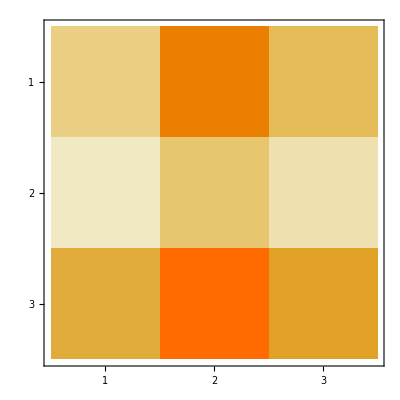

```mathematica
For[i=1,i≤iter,i++,
For[j=1,j≤Length[Bmatrix2[1][[i]]],j++,
For[k=1,k≤Length[Bmatrix2[1][[i,j]]],k++,
If[i==1,
stdprep[j,k]={}
];
stdprep[j,k]=Join[stdprep[j,k],{Bmatrix2[1][[i,j,k]]}]
]
];
]
For[l=1,l≤iter,l++,
For[m=1,m≤Length[Bmatrix2[1][[l]]],m++,
For[n=1,n≤Length[Bmatrix2[1][[l,m]]],n++,
stdfunc[m,n]=StandardDeviation[stdprep[m,n]];
meanfunc[m,n]=Mean[stdprep[m,n]]
]
]
]
stdarray=Array[stdfunc,{3,3}];
meanarray=Array[meanfunc,{3,3}];
MatrixPlot[stdarray]
```

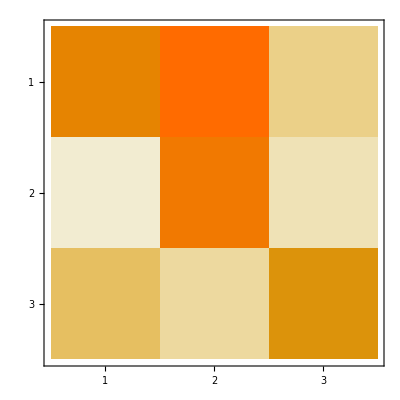

```mathematica
MatrixPlot[Abs[Bmatrix[1]-meanarray]]
```

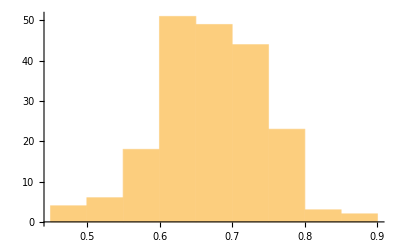

0.674151

0.707983

```mathematica
Histogram[stdprep[1,1]]
meanarray[[1,1]]
Bmatrix[1][[1,1]]
```

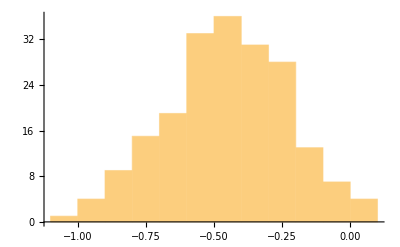

-0.453226

-0.407981

```mathematica
Histogram[stdprep[1,2]]
meanarray[[1,2]]
Bmatrix[1][[1,2]]
```

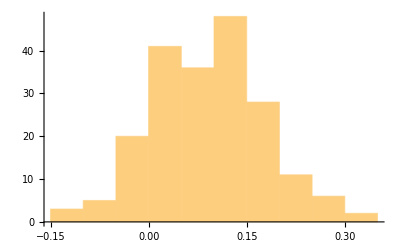

0.0914148

0.0861775

```mathematica
Histogram[stdprep[1,3]]
meanarray[[1,3]]
Bmatrix[1][[1,3]]
```

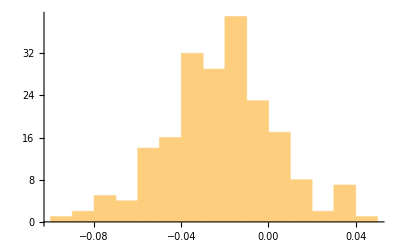

-0.0223028

-0.0227186

```mathematica
Histogram[stdprep[2,1]]
meanarray[[2,1]]
Bmatrix[1][[2,1]]
```

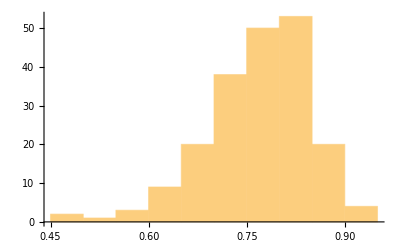

0.7713

0.80994

```mathematica
Histogram[stdprep[2,2]]
meanarray[[2,2]]
Bmatrix[1][[2,2]]
```

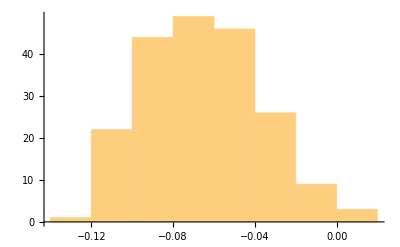

-0.0654208

-0.0627321

```mathematica
Histogram[stdprep[2,3]]
meanarray[[2,3]]
Bmatrix[1][[2,3]]
```

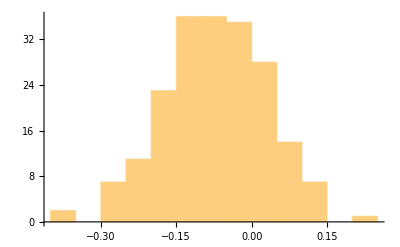

-0.0715374

-0.061149

```mathematica
Histogram[stdprep[3,1]]
meanarray[[3,1]]
Bmatrix[1][[3,1]]
```

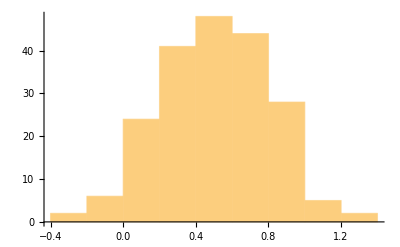

0.502163

0.506034

```mathematica
Histogram[stdprep[3,2]]
meanarray[[3,2]]
Bmatrix[1][[3,2]]
```

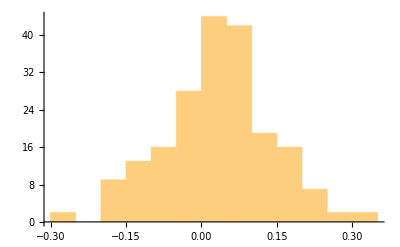

0.0328916

0.060775

```mathematica
Histogram[stdprep[3,3]]
meanarray[[3,3]]
Bmatrix[1][[3,3]]
```

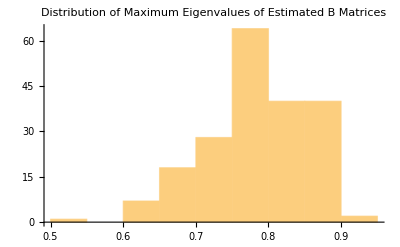

0.784158

0.820138

```mathematica
maxeiglist={};
For[i=1,i≤Length[Bmatrix2[1]],i++,
maxeiglist=Join[maxeiglist,{Max[Re[Eigenvalues[Bmatrix2[1][[i]]]]]}]
]
Histogram[maxeiglist,PlotLabel-> "Distribution of Maximum Eigenvalues of Estimated B Matrices"]
Mean[maxeiglist]
Max[Re[Eigenvalues[Bmatrix[1]]]]
```

```mathematica
Et[1]
RandomVariate[MultinormalDistribution[covar[1][[1]]],maxt]
```

{{1.55475,0.0872698,0.00109295},{-2.28348,-0.628481,-7.13473},{-2.3889,-0.146802,-1.81219},{-1.75804,0.658622,-1.10267},{-1.90197,0.321751,2.9877},{2.84449,-0.0924423,-2.76613},{0.269591,0.844267,1.84856},{-2.40297,0.277869,0.176566},{0.30411,1.14548,-0.351785},{0.435892,-1.11664,1.88564},{0.748141,-0.187104,0.0808113},{0.192879,-0.454221,-0.36666},{0.680352,-0.426119,-1.60606},{-0.834413,-1.53014,-2.13581},{-0.0453719,-0.172662,-1.89967},{-1.06241,-0.401125,-2.74062},{2.96839,0.599973,2.92434},{-1.20569,0.841684,1.52489},{-0.19988,0.498214,5.37989},{2.71296,0.0921359,-3.02539},{0.0911076,-0.789602,2.04853},{-1.01892,-0.618559,1.06832},{2.06245,-0.576147,1.49907},{3.0855,0.527989,-1.25165},{0.40975,-0.951257,-2.45192},{-3.42966,0.210107,0.685737},{1.31905,-0.515635,0.295676},{2.2742,-0.688489,-1.55055},{-0.721787,-0.968495,-1.89038},{-2.27494,0.108088,1.302},{1.17993,-0.506162,4.9123},{2.44694,0.40528,-1.04912},{0.299611,0.065924,-1.02991},{0.264013,-1.39532,1.66156},{-2.19065,-0.331942,-0.151043},{-1.5898,-0.268934,0.673447},{-2.77309,0.999485,3.68873},{0.446348,-1.49037,0.46591},{4.11529,-0.730807,-2.71563},{0.699759,0.985093,0.124423},{-0.355946,0.510618,0.299139},{-1.25285,-0.426787,-2.4219},{-1.41384,0.763119,0.3578},{0.480528,0.175616,-3.65552},{-1.3492,-0.00179008,-2.48555},{-0.72064,-0.572847,-1.03264},{4.06128,1.10653,0.0740915},{-0.223416,-0.736232,-0.695594},{-1.23914,1.53423,2.6678},{-3.0461,-0.0273348,0.557966},{1.83719,0.707303,0.834334},{-1.96502,0.0792739,-0.783265},{0.435434,-0.261755,0.161007},{1.82912,0.234639,0.462149},{0.27497,-0.589265,-0.193593},{-0.44032,0.203063,-1.49334},{-0.647026,0.60668,-1.77943},{-4.98214,-0.728331,-2.57536},{4.48436,-0.884419,1.48822},{-2.24551,0.81404,0.831776},{-4.4323,0.445464,-0.829719},{2.11566,0.639647,0.517539},{-0.921457,-0.00540105,-2.85949},{1.60516,-0.651198,2.5414},{2.52111,0.716834,3.45513},{0.167041,-0.13897,-0.33464},{1.48955,0.331188,1.80904},{-2.34327,0.498396,1.64145},{-1.88145,0.182574,-0.493963},{1.63734,-1.35561,-1.58683},{-1.15135,-0.392121,-2.99968},{3.13366,-0.306419,-2.49345},{-3.71912,0.197891,7.14361},{-3.04025,-0.457089,-4.16863},{-2.97958,-0.923965,0.504929},{-2.56826,-0.54694,-5.13948},{0.953819,0.370322,2.0587},{1.0195,-0.0216331,-0.432745},{0.575494,1.41911,3.3726},{-0.353736,1.04858,1.07535},{1.36392,0.907074,0.461696},{-1.99353,0.341131,-1.02451},{-0.0181623,0.540568,0.195669},{0.326875,0.0700737,-1.21949},{0.0619534,-0.133298,2.22031},{1.81637,-0.24514,-0.00913822},{3.46484,-0.143485,4.91983},{-1.46852,-0.552889,-4.54072},{2.50949,0.404461,-1.30033},{-1.33728,0.945183,0.561192},{3.18974,-0.648478,-3.86507},{-0.525312,0.0602262,-2.25251},{0.227828,0.525521,-2.01072},{1.32842,0.144766,5.61873},{-1.88595,0.637092,0.25804},{2.92336,-0.545171,-2.50804},{-0.14613,0.0268908,1.04211},{-2.43292,-1.60278,-2.10706},{-0.497522,-0.405978,-3.60218},{1.61137,-0.45768,0.331048}}

{{-1.54245,0.507065,1.98455},{4.8963,0.704963,-0.523413},{0.241243,-0.235609,-1.52753},{-2.9461,0.497575,0.388447},{0.759304,-0.0500371,0.997075},{-2.33316,0.544738,-0.68763},{-0.191204,-0.581911,2.2561},{3.54417,-0.298621,0.995017},{-0.138405,-0.654831,-2.79249},{1.3129,-0.618651,-3.52613},{-0.772174,0.769605,-5.09085},{1.74007,-0.811951,1.43885},{2.41359,0.315639,2.16971},{-2.51436,-0.12203,-1.56492},{-1.51254,0.14453,-0.135599},{0.267485,0.179097,-0.90164},{1.60235,-0.42156,0.829417},{1.45508,0.0407581,2.00869},{-3.34392,0.504011,-0.974976},{-0.986613,-0.478567,-2.59716},{-1.10649,1.00461,-2.12748},{-2.10964,-0.585716,1.01093},{3.85048,1.22272,4.75414},{-0.800124,-0.477983,-1.87311},{-0.94003,-0.285374,-2.43343},{2.24979,1.36228,4.00043},{-0.153623,0.942941,-3.72783},{-1.86596,-0.247132,2.32868},{-0.779129,-0.835145,-4.53274},{3.5475,-0.142563,0.877167},{-0.918473,1.25054,2.0019},{2.46052,-0.0751714,-2.26287},{1.21937,1.09811,0.0372053},{-0.0245604,-0.734871,0.594913},{2.91574,-0.160764,-0.313423},{2.61659,-0.459254,1.18095},{-2.20233,-0.295036,-0.547083},{0.83447,-0.30955,-1.31638},{1.27005,0.3635,3.77434},{0.167128,-0.0911541,-0.801092},{0.463704,0.723515,1.47964},{1.8133,-0.0305312,2.09617},{-1.06925,0.276651,-1.45827},{-0.328989,-0.510021,-1.57527},{0.874347,1.22172,1.49805},{-1.74017,0.0661443,2.05323},{-0.462528,0.768949,2.43437},{-2.24196,0.312694,-1.02388},{-2.61263,-0.191504,3.20327},{2.3177,0.163176,0.204366},{0.585599,0.0929652,-1.20645},{-0.289367,0.350357,1.71745},{-2.27868,0.209687,3.34391},{0.864515,-0.138065,-1.45184},{-3.73974,-0.08472,2.46972},{0.890372,0.287632,1.90476},{1.09329,1.19021,-1.42678},{-0.743333,0.828164,-6.89768},{1.33989,0.36713,0.726181},{-0.402558,0.852172,-0.160777},{0.617964,-0.152176,4.93016},{2.0796,0.285025,5.26837},{-0.132894,1.07635,0.880353},{-0.65615,0.257794,-3.79665},{-0.322792,-0.460233,-3.80473},{4.02639,-0.897431,-3.14016},{-2.29912,-0.91286,-1.28024},{-3.89352,0.380539,1.27135},{-1.47492,-0.242387,-0.913582},{-1.4535,-0.858802,-0.813068},{1.31924,-0.462942,-2.78805},{-0.223422,1.23451,4.87364},{2.35519,-0.473991,-2.31242},{2.02925,0.685734,1.85018},{1.52811,-0.155365,-0.504341},{-0.247269,0.333905,-0.325409},{0.112839,-0.148822,-2.58082},{1.36914,0.0968122,-2.03142},{-1.79903,-0.723092,-5.61789},{-0.755362,0.50814,-5.28257},{-4.12872,-0.173978,0.814253},{2.5061,0.67796,-0.676383},{4.35166,-0.118615,1.98109},{1.98764,0.898313,-1.41645},{1.35338,0.070369,-0.283771},{-1.43363,-0.508336,-1.03957},{-3.0045,0.497578,0.459767},{1.36641,-0.464172,-0.976403},{-3.42596,0.145054,-2.73698},{2.96493,-0.741635,1.74225},{1.98706,-0.0974728,-1.2995},{0.136246,0.391883,-1.2299},{-0.642403,0.661837,0.375756},{-1.48526,-0.108438,1.9745},{-4.39712,-0.89821,-0.814659},{-1.72463,0.546576,-2.79887},{-0.646128,0.340839,2.12563},{1.0209,0.423583,1.01924},{0.908662,0.42332,0.179919},{-1.28632,-0.281353,-3.61126}}